Вариант 4

(0 | 0.
3/5 | 0.10896
6/5 | 0.28579
9/5 | 0.392638
12/5 | 0.434786
3 | 0.443231
18/5 | 0.436737
21/5 | 0.42422
24/5 | 0.409698
27/5 | 0.394953
6 | 0.380757)

InterpolatingFunction[…]

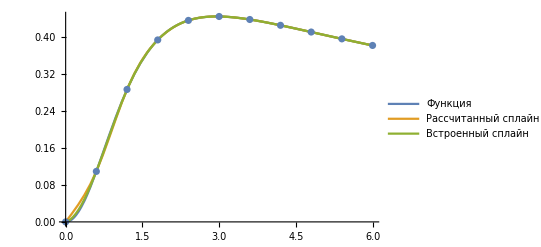

График погрешностей для рассчитанного и программного сплайна сплайна

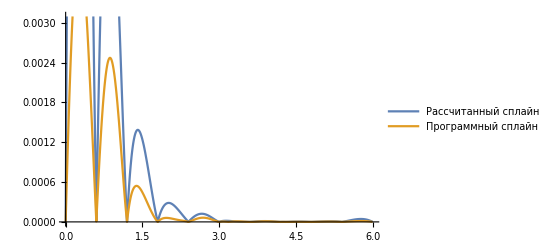

```mathematica
"Вариант 4"
f[x_] :=x^2/(√(2+x^2+√((2+x^2)^5)));
n =10; begin =0; end =6;step=(end-begin)/n;
Array[xdata,n+1,0];Array[ydata,n+1,0];
Array[h,n,0];Array[w,n,0];Array[{p,q,r,b},n,1];
(*Вычисление узлов сплайна*)
For[i=0,i<n+1,i++,
xdata[i]=begin+i*step;
ydata[i]=f[xdata[i]];];
(*Расчёт коэффициентов сплайна*)
For[i=0,i<n+1,i++,h[i]=xdata[i+1]-xdata[i];
w[i]=ydata[i+1]-ydata[i]];
p[1]=0;r[n]=0;
For[i=1,i<n+1,i++,
p[i]=h[i-1];
r[i]=h[i];
q[i]=2*(h[i]+h[i-1]);
b[i]=3*(w[i]/h[i]-w[i-1]/h[i-1])];
Array[u,n,1];Array[v,n,1];
Array[cs,n,0];
u[1]=(-r[1])/q[1];v[1]=b[1]/q[1];
For[i=2,i<n,i++,s=q[i]+p[i]*u[i-1];
u[i]=-r[i]/s;
v[i]=(b[i]-p[i]*v[i-1])/s];
cs[0]=0;cs[n]=0;
For[i=n-1,i>=1,i--,cs[i]=u[i]*cs[i+1]+v[i]];
(*Расчёт остальных коэффициентов сплайна*)
spln[xdata_,ydata_,cs_,n_,x_]:=
Block[{i=0,h1,a,b,c,d,t},While[x>xdata[i+1],i++];
h1=xdata[i+1]-xdata[i];
a=ydata[i];
b=(ydata[i+1]-ydata[i])/h1-(cs[i+1]+2*cs[i])*h1/3;
c =cs[i];
d=(cs[i+1]-cs[i])/(3*h1);
t=x-xdata[i];
Return[a+b*t+c*t^2+d*t^3]];
sq[x_]:=spln[xdata,ydata,cs,n,x](*Функция сплайна*)
data1=Table[{xdata[i],N[ydata[i]]},{i,0,n}];

MatrixForm[data1](*Вывод узлов*)
sp=Interpolation[data1,Method->"Spline"](*Встроенная сплайн-интерполяция*)
gr3:=Plot[{f[x],sq[x],sp[x]},{x,xdata[0],xdata[n]},
PlotLegends->{"Функция", "Рассчитанный сплайн","Встроенный сплайн"}]
gr2:=ListPlot[data1]
Show[{gr3,gr2}]
"График погрешностей для рассчитанного и программного сплайна сплайна"
grerr:=Plot[{Abs[sq[x]-f[x]],Abs[sp[x]-f[x]]},{x,xdata[0],xdata[n]},PlotLegends->{"Рассчитанный сплайн","Программный сплайн"}]
Show[grerr]
```